## 0. MTZ

```mathematica
Δ1[r_]=-r^4/ℓ^2+(r-M)^2;
H1[r_]=l(l+1)+r^2 m +(2M)/r-(2 M^2)/r^2-(2 r^2)/ℓ^2;
```

```mathematica
m=(μ^2+ξ R)/.R->4 3/ℓ^2;
```

```mathematica
(*horizon*)
```

```mathematica
Solve[Δ1[r]==0,r]
```

{{r→1/2 (-ℓ-√ℓ √(4 M+ℓ))},{r→1/2 (-ℓ+√ℓ √(4 M+ℓ))},{r→1/2 (ℓ-√(-4 M ℓ+ℓ^2))},{r→1/2 (ℓ+√(-4 M ℓ+ℓ^2))}}

```mathematica
{1/2 (-ℓ+√ℓ √(4 M+ℓ)),1/2 (ℓ-√(-4 M ℓ+ℓ^2)),1/2 (ℓ+√(-4 M ℓ+ℓ^2))}/.ℓ->10/.M->1//N
```

{0.91608,1.12702,8.87298}

```mathematica
rh1=ℓ/2(1-√(1-(4M)/ℓ));
ri1=ℓ/2 (-1+√(1+(4 M)/ℓ));
rc1=ℓ/2 (1+√(1-(4 M)/ℓ));
```

```mathematica
Solve[rc1==rh1,M]
```

{{M→ℓ/4}}

```mathematica
Solve[ri1==rh1,M]
```

{{M→0}}

```mathematica
κp1=D[Δ[r]/r^2,r]/2/.r->rh/.Δ[rh]->0/.rh->rh1/.Δ->Δ1//FullSimplify
```

(√(1-(4 M)/ℓ))/ℓ

```mathematica
κm1=D[Δ[r]/r^2,r]/2/.Δ[r]->0/.Δ->Δ1/.r->ri1//FullSimplify
```

-(√(1+(4 M)/ℓ))/ℓ

```mathematica
κp1/.Δ->Δ1
```

(√(1-(4 M)/ℓ))/ℓ

```mathematica
2 (-M+rh)-(4 rh^3)/ℓ^2/.rh->rh1//FullSimplify
```

M (4-2 √(1-(4 M)/ℓ))+(-1+√(1-(4 M)/ℓ)) ℓ

```mathematica
{κp1/.Δ->Δ1/.rh->rh1,κp1/.Δ->Δ1/.rh->ri1}//FullSimplify
```

{(√(1-(4 M)/ℓ))/ℓ,(√(1-(4 M)/ℓ))/ℓ}

```mathematica
(*디멘션 레스로 고치고(RNdS참고), M에대한  Imω를 그려본다. Cardoso랑 consistent하게 나오나?  M이 작을때 invalid!!! M-> M/(√Λ),r... 모든 parameters를 1/(√Λ)*)(*or  다하고 Λ=1로 두고 해보기.*)
```

### Λ=1일때,

```mathematica
Clear[Λ];
Λ=1;
```

```mathematica
Module[{(*Λ,Mmax,*)Δ,rh,ℓ,ri,rc},
(*Λ=1;*)
ℓ=√(3/Λ);
rh=ℓ/2(1-√(1-(4M)/ℓ));
ri=ℓ/2 (-1+√(1+(4 M)/ℓ));
rc=ℓ/2 (1+√(1-(4 M)/ℓ));
Mmax=Solve[1-(4M)/ℓ==0,M][[1,1,2]];
{Subscript[M1, max]==Mmax,Subscript[r, i]==ri,Subscript[r, o]==rh,Subscript[r, c]==rc}/.M->Mmax//N
]
```

{M1_max==0.433013,r_i==0.358719,r_o==0.866025,r_c==0.866025}

```mathematica
Manipulate[Plot[(*Δ[r]=*)(-M+r)^2-r^4/ℓ^2/.ℓ->√(3/Λ),{r,0,1.5},AxesLabel->{"r","Δ[r]"}],{M,0,Mmax}]
(*rc=ro : M=ℓ/4; ri=ro : M=0*)
```

## 1. effective potential

```mathematica
Clear[m,Veff]
```

```mathematica
Veff[r_,ω_,l_,μ_,ξ_,M_]=ω^2-1/r^4(l(l+1)+r^2 (μ^2+ξ R1) +(2M)/r-(2 M^2)/r^2-(2 r^2)/ℓ^2)(-r^4/ℓ^2+(r-M)^2)/.R1->4 3/ℓ^2/.ℓ->√(3/Λ);
```

#### l 바꾸면서.

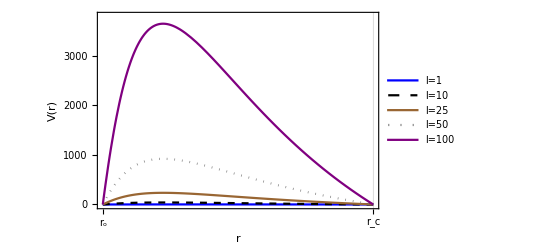

```mathematica
Module[{rh,rc,ω,(*l,*)μ,ξ,M},
ω=1;(*l=1;*)μ=1;ξ=1;M=0.3;
rh=ℓ/2(1-√(1-(4M)/ℓ))/.ℓ->√(3/Λ);
rc=ℓ/2 (1+√(1-(4 M)/ℓ))/.ℓ->√(3/Λ);
Plot[{-Veff[r,ω,1,μ,ξ,M],-Veff[r,ω,10,μ,ξ,M],-Veff[r,ω,25,μ,ξ,M],-Veff[r,ω,50,μ,ξ,M],-Veff[r,ω,100,μ,ξ,M]},{r,rh,rc},AxesOrigin->{rh,0},PlotLegends->Placed[{"l=1","l=10","l=25","l=50","l=100"},{Right,Top}],GridLines->{{{rc,{Dashed,Black}}},{}},PlotRange->{{rh,rc},{-10,3800}},PlotStyle->{Blue,{Black,Dashed},Brown,{Gray,Dotted},Purple},Frame->True,Axes->False,FrameLabel->{Style["r",15],Style["V(r)",13]},(*RotateLabel->False,*)FrameTicks->{{{0,1000,2000,3000},None},{{{rh,Style["r_o",12]},{rc,Style["r_c",12]}},None}}]]
```

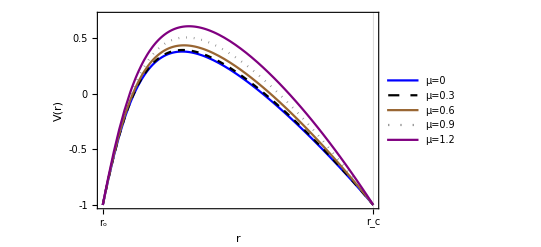

```mathematica
Module[{rh,rc,ω,l,(*μ,*)ξ,M},
ω=1;l=1;ξ=1;M=0.3;
rh=ℓ/2(1-√(1-(4M)/ℓ))/.ℓ->√(3/Λ);
rc=ℓ/2 (1+√(1-(4 M)/ℓ))/.ℓ->√(3/Λ);
Plot[{-Veff[r,ω,l,0,ξ,M],-Veff[r,ω,l,0.3,ξ,M],-Veff[r,ω,l,0.6,ξ,M],-Veff[r,ω,l,0.9,ξ,M],-Veff[r,ω,l,1.2,ξ,M]},{r,rh,rc},AxesOrigin->{rh,0},PlotLegends->Placed[{"μ=0","μ=0.3","μ=0.6","μ=0.9","μ=1.2"},{Right,Top}],PlotStyle->{Blue,{Black,Dashed},Brown,{Gray,Dotted},Purple},GridLines->{{{rc,{Dashed,Black}}},{}},PlotRange->{{rh,rc},{-1,0.7}},Frame->True,Axes->False,FrameLabel->{Style["r",15],Style["V(r)",13]},(*RotateLabel->False,*)FrameTicks->{{{-1,-0.5,0,0.5},None},{{{rh,Style["r_o",12]},{rc,Style["r_c",12]}},None}}]]
```

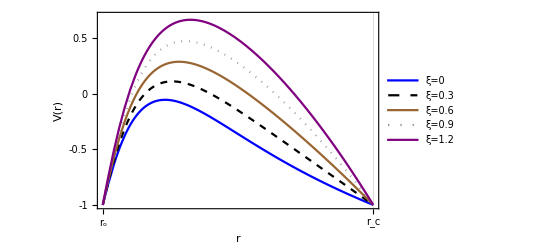

```mathematica
Module[{rh,rc,ω,l,μ,(*ξ,*)M},
ω=1;l=1;μ=1;M=0.3;
rh=ℓ/2(1-√(1-(4M)/ℓ))/.ℓ->√(3/Λ);
rc=ℓ/2 (1+√(1-(4 M)/ℓ))/.ℓ->√(3/Λ);
Plot[{-Veff[r,ω,l,μ,0,M],-Veff[r,ω,l,μ,0.3,M],-Veff[r,ω,l,μ,0.6,M],-Veff[r,ω,l,μ,0.9,M],-Veff[r,ω,l,μ,1.2,M]},{r,rh,rc},AxesOrigin->{rh,0},Frame->True,Axes->False,FrameLabel->{Style["r",15],Style["V(r)",13]},(*RotateLabel->False,*)PlotLegends->Placed[{"ξ=0","ξ=0.3","ξ=0.6","ξ=0.9","ξ=1.2"},{Right,Top}],PlotStyle->{Blue,{Black,Dashed},Brown,{Gray,Dotted},Purple},GridLines->{{{rc,{Dashed,Black}}},{}},PlotRange->{{rh,rc},{-1,0.7}},FrameTicks->{{{-1,-0.5,0,0.5},None},{{{rh,Style["r_o",12]},{rc,Style["r_c",12]}},None}}]]
```

## 2. M vs Imω

#### Imω in dS mode

```mathematica
ImωdS[n_,l_,μ_,ξ_]=Abs[-1/ℓ(2n+l+3/2-√(9/4+12ξ-ℓ^2 μ^2))/.ℓ->√(3/Λ)]
```

Abs[3/2+l+2 n-√(9/4-3 μ^2+12 ξ)]/(√3)

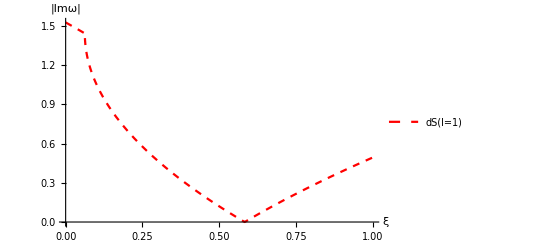

```mathematica
Plot[ImωdS[0,1,1,ξ],{ξ,0,1},PlotStyle->{{Red,Dashed}},AxesLabel->{"ξ","|Imω|"},PlotLegends->{"dS(l=1)"}]
```

```mathematica
Solve[ImωdSoverκm[0,1,ξ,μ]==1/2,ξ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ξ→InverseFunction[ImωdSoverκm,3,4][0,1,1/2,μ]}}

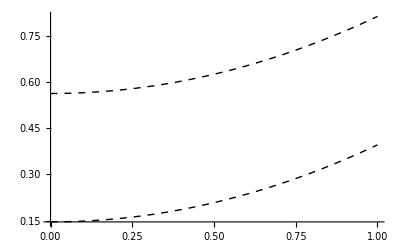

```mathematica
p1=Plot[{1/16 (9+4 μ^2),1/48 (7+12 μ^2)},{μ,0,1},PlotStyle->{{Thick,Dashed,Black},{Thick,Dashed,Black}}]
```

```mathematica
p2=ContourPlot[ImωdSoverκm[0,1,μ,ξ],{μ,0,1},{ξ,0,1},PlotRange->All,Contours->7,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->200,LegendFunction->(Framed[#,RoundingRadius->5]&),LegendLabel->("|Imω|")/("|κ_-|")],{After,Top}],ColorFunction->"CoolColors",FrameLabel->{Style["μ",15],Style["ξ",15]},RotateLabel->False]
```

ContourPlot::cfun: Value of option ColorFunction -> CoolColors is not a valid color function, or a gradient ColorData entity.

-Graphics-

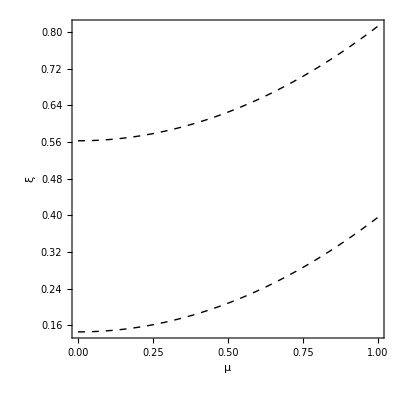

```mathematica
Show[{p2,p1}]
```

#### Reω and Imω in MTZ BH

```mathematica
Clear[Reω,Imω];
Reω[M_,n_,l_,μ_,ξ_]:=Module[{(*l,M,Λ,*)ℓ,DV,V,Δ,H,m,rh,ri,rc,D2V,D3V,D4V,D5V,D6V,mK2,mK3,ωω,V0,ωp,rp,κm},
(*l=1;*)(*M=0.01;*)
ℓ=√(3/Λ);
m=(μ^2+ξ R)/.R->4 3/ℓ^2;
(*n=0;*)
ri=ℓ/2 (-1+√(1+(4 M)/ℓ));
rh=ℓ/2(1-√(1-(4M)/ℓ));
rc=ℓ/2 (1+√(1-(4 M)/ℓ));
Δ[r_]=-r^4/ℓ^2+(r-M)^2;
H[r_]=l(l+1)+r^2 m +(2M)/r-(2 M^2)/r^2-(2 r^2)/ℓ^2;
V0=(H[r] Δ[r])/r^4;
V[r_]=ω^2-(H[r] Δ[r])/r^4;
DV=D[-V[r],r]*Δ[r]/r^2;
D2V=D[D[-V[r],r]*Δ[r]/r^2,r]*Δ[r]/r^2;
D3V=D[D[D[-V[r],r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2;
D4V=D[D[D[D[-V[r],r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2;
D5V=D[D[D[D[D[-V[r],r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2;
D6V=D[D[D[D[D[D[-V[r],r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2;
rp=NSolve[DV==0&&r>(rh+0.000000001)&&r<rc,r,Reals][[1,1,2]]//N;
mK2=1/(√(2*D2V))*((1+(2*n+1)^2)/32*D4V/(D2V)-(28+60*(2*n+1)^2)/1152*(D3V/D2V)^2);
mK3=(n+1/2)/(2*D2V)*(5/6912*(D3V/D2V)^4*(77+188*(n+1/2)^2)-1/384*((D3V^2*D4V)/D2V^3)*(51+100*(n+1/2)^2)+1/2304*(D4V/D2V)^2*(67+68*(n+1/2)^2)+1/288*((D3V*D5V)/D2V^2)*(19+28*(n+1/2)^2)-1/288*(D6V/D2V)*(5+4*(n+1/2)^2));
ωω=V0+√(2D2V)mK2/I-I (n+1/2)√(2D2V)(1+mK3/(n+1/2));
ωp=√ωω;
κm=D[Δ[r]/r^2,r]/2/.r->ri;
(*{D2V,D3V,D4V,D5V,D6V,mK2,mK3,ωω,ωp,Im[ωp]}/.r->rp//N*)
Re[ωp/.r->rp]
]
Imω[M_,n_,l_,μ_,ξ_]:=Module[{(*l,M,Λ,*)ℓ,DV,V,Δ,H,m,rh,ri,rc,D2V,D3V,D4V,D5V,D6V,mK2,mK3,ωω,V0,ωp,rp,κm},
(*l=1;*)(*M=0.01;*)
ℓ=√(3/Λ);
m=(μ^2+ξ R)/.R->4 3/ℓ^2;
(*n=0;*)
ri=ℓ/2 (-1+√(1+(4 M)/ℓ));
rh=ℓ/2(1-√(1-(4M)/ℓ));
rc=ℓ/2 (1+√(1-(4 M)/ℓ));
Δ[r_]=-r^4/ℓ^2+(r-M)^2;
H[r_]=l(l+1)+r^2 m +(2M)/r-(2 M^2)/r^2-(2 r^2)/ℓ^2;
V0=(H[r] Δ[r])/r^4;
V[r_]=ω^2-(H[r] Δ[r])/r^4;
DV=D[-V[r],r]*Δ[r]/r^2;
D2V=D[D[-V[r],r]*Δ[r]/r^2,r]*Δ[r]/r^2;
D3V=D[D[D[-V[r],r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2;
D4V=D[D[D[D[-V[r],r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2;
D5V=D[D[D[D[D[-V[r],r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2;
D6V=D[D[D[D[D[D[-V[r],r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2;
rp=NSolve[DV==0&&r>(rh+0.000000001)&&r<rc,r,Reals][[1,1,2]]//N;
mK2=1/(√(2*D2V))*((1+(2*n+1)^2)/32*D4V/(D2V)-(28+60*(2*n+1)^2)/1152*(D3V/D2V)^2);
mK3=(n+1/2)/(2*D2V)*(5/6912*(D3V/D2V)^4*(77+188*(n+1/2)^2)-1/384*((D3V^2*D4V)/D2V^3)*(51+100*(n+1/2)^2)+1/2304*(D4V/D2V)^2*(67+68*(n+1/2)^2)+1/288*((D3V*D5V)/D2V^2)*(19+28*(n+1/2)^2)-1/288*(D6V/D2V)*(5+4*(n+1/2)^2));
ωω=V0+√(2D2V)mK2/I-I (n+1/2)√(2D2V)(1+mK3/(n+1/2));
ωp=√ωω;
κm=D[Δ[r]/r^2,r]/2/.r->ri;
(*{D2V,D3V,D4V,D5V,D6V,mK2,mK3,ωω,ωp,Im[ωp]}/.r->rp//N*)
Im[ωp/.r->rp]
]
```

### μ=1 and ξ=1, n=0, l=1,10,25,50,100

#### Imω

```mathematica
Clear[T01,T010,T025,T050,T0100];
```

```mathematica
T01=Table[{M,Imω[M,0,1,1,1]},{M,0.0001,0.01,0.0001}];
T010=Table[{M,Imω[M,0,10,1,1]},{M,0.0001,0.01,0.0001}];
T025=Table[{M,Imω[M,0,25,1,1]},{M,0.0001,0.01,0.0001}];
T050=Table[{M,Imω[M,0,50,1,1]},{M,0.0001,0.01,0.0001}];
```

```mathematica
T0100=Table[{M,Imω[M,0,100,1,1]},{M,0.001,0.01,0.0001}];
```

```mathematica
T0100α=Table[{M,Imω[M,0,100,1,1]},{M,0.00001,0.001,0.00002}];
```

```mathematica
T025α=Table[{M,Imω[M,0,25,1,1]},{M,0.00001,0.001,0.00002}];
```

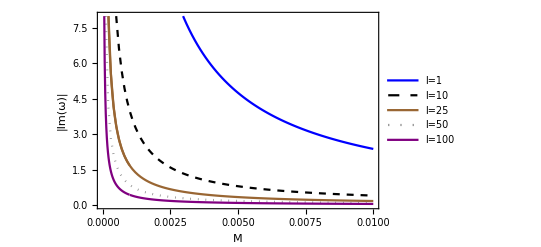

```mathematica
ListPlot[{T01,T010,T025,T050,T0100,T0100α,T025α},FrameLabel->{Style["M",12],Style["|Im(ω)|",12]},AxesOrigin->{0,0},PlotRange->{{0,0.01},{0,8}},Frame->True,Axes->False,PlotStyle->{Blue,{Black,Dashed},Brown,{Gray,Dotted},Purple,Purple,Brown},PlotLegends->Placed[{"l=1","l=10","l=25","l=50","l=100"},{Right,Top}],Joined->True(*,Ticks->{{0,(*{0.00075,"M_c"},*)0.002,0.004,0.006,0.008,0.010},{0.5(*,{ImωdS[1,0,0],"Imω_dS"}*),1}}*)(*,GridLines->{{{0.00075,{Dashed,Black}}},{{ImωdS[1,0,0],{Dashed,Black}}}}*)(*,PlotLegends->{(*"l=1","l=10",*)"PS mode : l=100,μ=0,ξ=0"}*)]
```

#### Reω

```mathematica
Clear[R01,R010,R025,R050,R0100];
```

```mathematica
R010=Table[{M,Reω[M,0,10,1,1]},{M,0.0001,0.01,0.0001}];
R025=Table[{M,Reω[M,0,25,1,1]},{M,0.0001,0.01,0.0001}];
R050=Table[{M,Reω[M,0,50,1,1]},{M,0.0001,0.01,0.0001}];
R0100=Table[{M,Reω[M,0,100,1,1]},{M,0.0001,0.01,0.0001}];
```

```mathematica
R01=Table[{M,Reω[M,0,1,1,1]},{M,0.001,0.01,0.0001}];
```

```mathematica
R01α=Table[{M,Reω[M,0,1,1,1]},{M,0.00001,0.001,0.00002}];
```

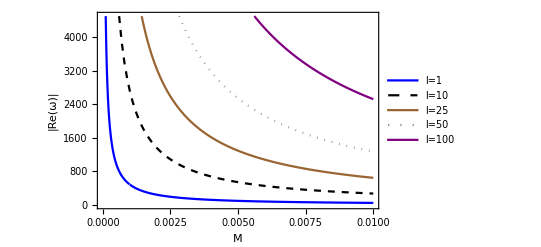

```mathematica
ListPlot[{R01,R010,R025,R050,R0100,R01α},FrameLabel->{Style["M",12],Style["|Re(ω)|",12]},AxesOrigin->{0,0},PlotRange->{{0,0.01},{0,4500}},Frame->True,Axes->False,PlotStyle->{Blue,{Black,Dashed},Brown,{Gray,Dotted},Purple,Blue},PlotLegends->Placed[{"l=1","l=10","l=25","l=50","l=100"},{Right,Top}],Joined->True(*,Ticks->{{0,(*{0.00075,"M_c"},*)0.002,0.004,0.006,0.008,0.010},{0.5(*,{ImωdS[1,0,0],"Imω_dS"}*),1}}*)(*,GridLines->{{{0.00075,{Dashed,Black}}},{{ImωdS[1,0,0],{Dashed,Black}}}}*)(*,PlotLegends->{(*"l=1","l=10",*)"PS mode : l=100,μ=0,ξ=0"}*)]
```

### μ=1 and ξ=1, l=1, n=0,1,2,5,10

#### Imω

```mathematica
Clear[T01,T10,T20,T50,T100,T00,T20α,T00α];
```

```mathematica
T10=Table[{M,Imω[M,1,1,1,1]},{M,0.0001,0.01,0.0001}];
T50=Table[{M,Imω[M,5,1,1,1]},{M,0.0001,0.01,0.0001}];
T100=Table[{M,Imω[M,10,1,1,1]},{M,0.0001,0.01,0.0001}];
```

```mathematica
T00=Table[{M,Imω[M,0,1,1,1]},{M,0.001,0.01,0.0001}];
T20=Table[{M,Imω[M,2,1,1,1]},{M,0.001,0.01,0.0001}];
```

```mathematica
T20α=Table[{M,Imω[M,2,1,1,1]},{M,0.00001,0.001,0.00002}];
T00α=Table[{M,Imω[M,0,1,1,1]},{M,0.00001,0.001,0.00002}];
```

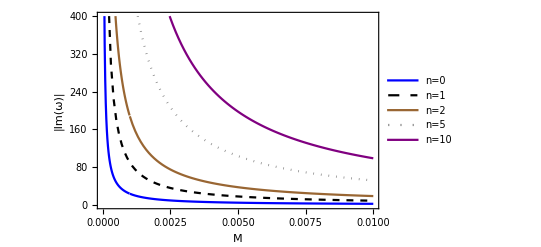

```mathematica
ListPlot[{T00,T10,T20,T50,T100,T00α,T20α},FrameLabel->{Style["M",12],Style["|Im(ω)|",12]},AxesOrigin->{0,0},PlotRange->{{0,0.01},{0,400}},Frame->True,Axes->False,PlotStyle->{Blue,{Black,Dashed},Brown,{Gray,Dotted},Purple,Blue,Brown},PlotLegends->Placed[{"n=0","n=1","n=2","n=5","n=10"},{Right,Top}],Joined->True(*,Ticks->{{0,(*{0.00075,"M_c"},*)0.002,0.004,0.006,0.008,0.010},{0.5(*,{ImωdS[1,0,0],"Imω_dS"}*),1}}*)(*,GridLines->{{{0.00075,{Dashed,Black}}},{{ImωdS[1,0,0],{Dashed,Black}}}}*)(*,PlotLegends->{(*"l=1","l=10",*)"PS mode : l=100,μ=0,ξ=0"}*)]
```

#### Reω

```mathematica
Clear[R00,R10,R20,R50,R100,R00α,R20α];
```

```mathematica
R10=Table[{M,Reω[M,1,1,1,1]},{M,0.0001,0.01,0.0001}];
R50=Table[{M,Reω[M,5,1,1,1]},{M,0.0001,0.01,0.0001}];
R100=Table[{M,Reω[M,10,1,1,1]},{M,0.0001,0.01,0.0001}];
```

```mathematica
R00=Table[{M,Reω[M,0,1,1,1]},{M,0.001,0.01,0.0001}];
R00α=Table[{M,Reω[M,0,1,1,1]},{M,0.00001,0.001,0.00002}];
R20=Table[{M,Reω[M,2,1,1,1]},{M,0.001,0.01,0.0001}];
R20α=Table[{M,Reω[M,2,1,1,1]},{M,0.00001,0.001,0.00002}];
```

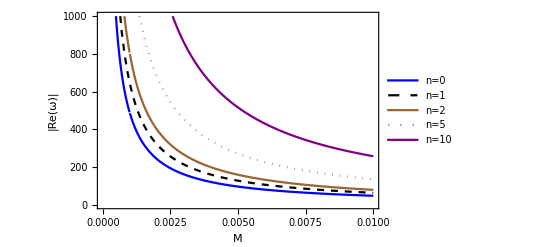

```mathematica
ListPlot[{R00,R10,R20,R50,R100,R00α,R20α},FrameLabel->{Style["M",12],Style["|Re(ω)|",12]},AxesOrigin->{0,0},PlotRange->{{0,0.01},{0,1000}},Frame->True,Axes->False,PlotStyle->{Blue,{Black,Dashed},Brown,{Gray,Dotted},Purple,Blue,Brown},PlotLegends->Placed[{"n=0","n=1","n=2","n=5","n=10"},{Right,Top}],Joined->True(*,Ticks->{{0,(*{0.00075,"M_c"},*)0.002,0.004,0.006,0.008,0.010},{0.5(*,{ImωdS[1,0,0],"Imω_dS"}*),1}}*)(*,GridLines->{{{0.00075,{Dashed,Black}}},{{ImωdS[1,0,0],{Dashed,Black}}}}*)(*,PlotLegends->{(*"l=1","l=10",*)"PS mode : l=100,μ=0,ξ=0"}*)]
```

## 3. Spectral gap Imω/(κ_-)

### PT

```mathematica
Clear[PT]
```

```mathematica
PT[M_]=1/2 κp1/Abs[κm1]/.ℓ->√(3/Λ)
```

(√(1-(4 M)/(√3)))/(2 √Abs[1+(4 M)/(√3)])

### Imω/κ_- in dS mode

```mathematica
ImωdSoverκm[M_,n_,l_,μ_,ξ_]=ImωdS[n,l,μ,ξ]/((√(1+(4 M)/ℓ))/ℓ)/.ℓ->√(3/Λ)//FullSimplify
```

Abs[3/2+l+2 n-√(9/4-3 μ^2+12 ξ)]/(√(1+(4 M)/(√3)))

```mathematica
ImωdSoverκm[0,0,1,μ,ξ]
```

Abs[5/2-√(9/4-3 μ^2+12 ξ)]

```mathematica
Solve[ImωdSoverκm[0,0,1,μ,ξ]==(1/2),ξ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ξ→1/16 (9+4 μ^2)},{ξ→1/48 (7+12 μ^2)}}

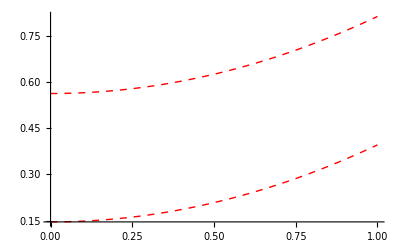

```mathematica
p1=Plot[{1/16 (9+4 μ^2),1/48 (7+12 μ^2)},{μ,0,1},PlotStyle->{{Thick,Dashed,Red},{Thick,Dashed,Red}}]
```

```mathematica
Clear[p2]
```

```mathematica
CoolColor[ z_ ] :=RGBColor[z,1-z,1];
```

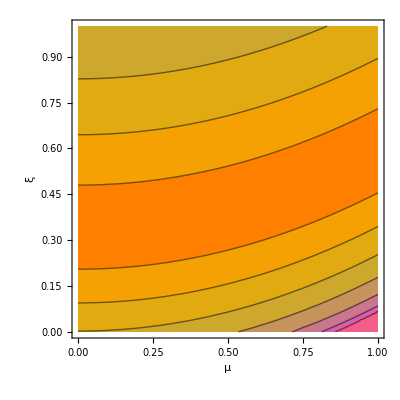

```mathematica
p2=ContourPlot[ImωdSoverκm[0,0,1,μ,ξ],{μ,0,1},{ξ,0,1},PlotRange->All,Contours->7,ColorFunction->"FruitPunchColors",PlotLegends->{Placed[BarLegend[Automatic,LegendMarkerSize->200,LegendFunction->(Framed[#,RoundingRadius->5]&),LegendLabel->Style[("|Im(ω)|")/("κ_i"),15]],{After,Top}]},FrameLabel->{Style["μ",15],Style["ξ",15]}(*,RotateLabel->False*)]
```

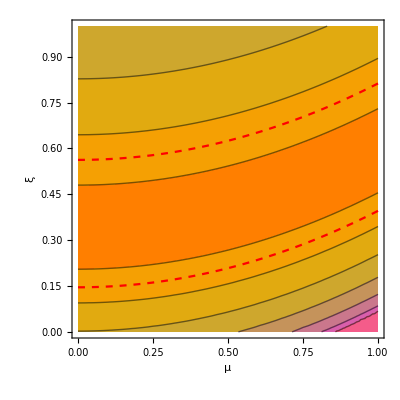

```mathematica
Show[{p2,p1}](*F1- ColorSchemes- 색상 명령어 참고하기.*)
```

### Imω/κ_- in MTZ BH

```mathematica
Clear[α];
(*Imω/(κ_-)=*)α[M_,l_,μ_,ξ_]:=Module[{(*l,M,Λ,*)ℓ,DV,V,Δ,H,m,rh,ri,rc,D2V,D3V,D4V,D5V,D6V,mK2,mK3,n,ωω,V0,ωp,rp,κm},
(*l=1;*)(*M=0.01;*)
ℓ=√(3/Λ);
m=(μ^2+ξ R)/.R->4 3/ℓ^2;
n=0;
ri=ℓ/2 (-1+√(1+(4 M)/ℓ));
rh=ℓ/2(1-√(1-(4M)/ℓ));
rc=ℓ/2 (1+√(1-(4 M)/ℓ));
Δ[r_]=-r^4/ℓ^2+(r-M)^2;
H[r_]=l(l+1)+r^2 m +(2M)/r-(2 M^2)/r^2-(2 r^2)/ℓ^2;
V0=(H[r] Δ[r])/r^4;
V[r_]=ω^2-(H[r] Δ[r])/r^4;
DV=D[-V[r],r]*Δ[r]/r^2;
D2V=D[D[-V[r],r]*Δ[r]/r^2,r]*Δ[r]/r^2;
D3V=D[D[D[-V[r],r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2;
D4V=D[D[D[D[-V[r],r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2;
D5V=D[D[D[D[D[-V[r],r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2;
D6V=D[D[D[D[D[D[-V[r],r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2,r]*Δ[r]/r^2;
rp=NSolve[DV==0&&r>(rh+0.000000001)&&r<rc,r,Reals][[1,1,2]]//N;
mK2=1/(√(2*D2V))*((1+(2*n+1)^2)/32*D4V/(D2V)-(28+60*(2*n+1)^2)/1152*(D3V/D2V)^2);
mK3=(n+1/2)/(2*D2V)*(5/6912*(D3V/D2V)^4*(77+188*(n+1/2)^2)-1/384*((D3V^2*D4V)/D2V^3)*(51+100*(n+1/2)^2)+1/2304*(D4V/D2V)^2*(67+68*(n+1/2)^2)+1/288*((D3V*D5V)/D2V^2)*(19+28*(n+1/2)^2)-1/288*(D6V/D2V)*(5+4*(n+1/2)^2));
ωω=V0+√(2D2V)mK2/I-I (n+1/2)√(2D2V)(1+mK3/(n+1/2));
ωp=√ωω;
κm=D[Δ[r]/r^2,r]/2/.r->ri;
(*{D2V,D3V,D4V,D5V,D6V,mK2,mK3,ωω,ωp,Im[ωp]}/.r->rp//N*)
Im[ωp/.r->rp]/Abs[κm]
]
```

#### Case of SCC violation ξ=1, μ=1

```mathematica
Clear[α11,α112]
α11=Table[{M,α[M,(*l*)100,(*μ*)1,(*ξ*)1]},{M,0.0001,0.003,0.0001}];
α112=Table[{M,α[M,(*l*)100,(*μ*)1,(*ξ*)1]},{M,0.003,0.01,0.0005}];
```

```mathematica
α113=Table[{M,α[M,(*l*)100,(*μ*)1,(*ξ*)1]},{M,0.01,Mmax,0.003}];
```

```mathematica
α11Max=Table[{M,α[M,(*l*)100,(*μ*)1,(*ξ*)1]},{M,0.4,0.43,0.001}];
```

```mathematica
α11Max1=Table[{M,α[M,(*l*)100,(*μ*)1,(*ξ*)1]},{M,0.43,Mmax,0.0001}];
```

```mathematica
Mmax//N
```

0.433013

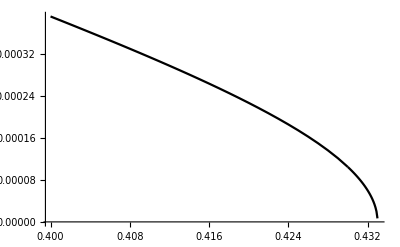

```mathematica
plotinWKBMax=ListPlot[{α11Max,α11Max1},(*PlotRange->{{0.4,Mmax},{-0.01,1}},*)(*FrameLabel->{Style["M",15],Style["|Re(ω)|",15]},AxesOrigin->{0,0},Frame->True,Axes->False,*)PlotStyle->{Black},Joined->True(*PlotLegends->Placed[{"l=1","l=10","l=25","l=50","l=100"},{Right,Top}],*)]
```

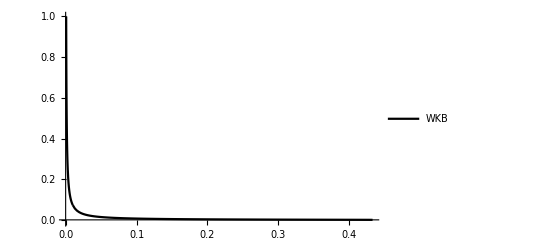

```mathematica
Clear[WKB1]
WKB1=ListPlot[{α11,α112,α113},PlotRange->{{0,Mmax},{-0.01,1}},(*FrameLabel->{Style["M",15],Style["|Re(ω)|",15]},AxesOrigin->{0,0},Frame->True,Axes->False,*)PlotStyle->{Black},Joined->True,PlotLegends->Placed[{"WKB"},{Right,Top}]]
```

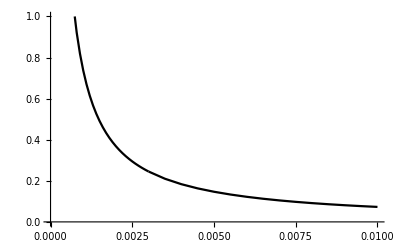

```mathematica
plotinWKBmin=ListPlot[{α11,α112},PlotRange->{{0,0.01},{0,1}},(*FrameLabel->{Style["M",15],Style["|Re(ω)|",15]},AxesOrigin->{0,0},Frame->True,Axes->False,*)PlotStyle->{Black},(*PlotLegends->Placed[{"l=1","l=10","l=25","l=50","l=100"},{Right,Top}],*)Joined->True]
```

```mathematica
plotindS=Plot[ImωdSoverκm[M,(*n*)0,(*l*)1,(*μ*)1,(*ξ*)1],{M,0,0.01},PlotRange->{{0,0.01},{0,1}},Frame->True,PlotStyle->{Red},FrameTicks->{{{0,0.5,1},None},{{0,0.005,0.01},None}},GridLines->{{},{{0.5,{Red,Dashed,Thin}}}},ImageSize->110]
```

-Graphics-

```mathematica
plotinPT=Plot[PT[M],{M,0.4,Mmax},PlotRange->{{0.4,Mmax+0.001},{-0.00005,0.0004}},Frame->True,PlotStyle->{Blue},FrameTicks->{{{0,0.0002,0.0004},None},{{0.4,0.41,0.42,0.43},None}},(*GridLines->{{{0.0255,Dashed}},{{0.0796776,Dashed}}},*)ImageSize->120,Epilog->{PointSize[Medium],Point[{{0.43301,3.0958442721023882*^-6}},VertexColors->{Blue}]}]
```

-Graphics-

```mathematica
plotinmin=Show[plotindS,plotinWKBmin]
```

-Graphics-

```mathematica
plotinMax=Show[plotinPT,plotinWKBMax]
```

-Graphics-

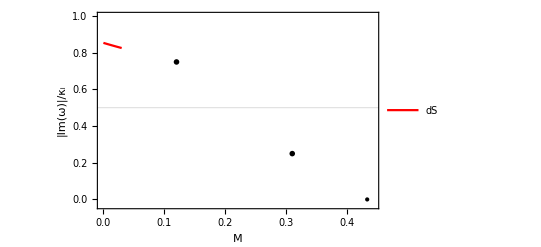

```mathematica
dS1=Plot[ImωdSoverκm[M,(*n*)0,(*l*)1,(*μ*)1,(*ξ*)1],{M,0,0.03},FrameLabel->{Style["M",12],Style["|Im(ω)|/κ_i",12]},(*RotateLabel->False,*)Frame->True,Axes->False,AxesOrigin->{0,0},PlotStyle->{Blue,Red},PlotRange->{{-0.001,Mmax+0.01},{-0.03,1}},GridLines->{{},{{0.5,{Red,Dashed,Thin}}}},Epilog->{(*Inset[Style["M_1",12],{0.12,-0.006}],*)Inset[plotinmin,{0.12,0.75}],Inset[plotinMax,{0.31,0.25}],{PointSize[Medium],Point[{{0.43301,3.0958442721023882*^-6}},VertexColors->{Blue}]}},PlotLegends->Placed[{"dS"},{Right,Top}]]
```

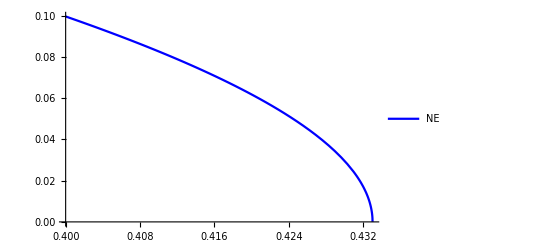

```mathematica
PT1=Plot[PT[M],{M,0.4,Mmax},PlotStyle->{Blue},PlotLegends->Placed[{"NE"},{Right,Top}]]
```

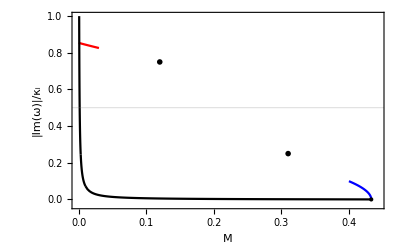

```mathematica
Show[dS1,WKB1,PT1]
```

#### Case of SCC valid ξ=0.5, μ=0.5

```mathematica
Clear[β11,β112]
β11=Table[{M,α[M,(*l*)100,(*μ*)0.5,(*ξ*)0.5]},{M,0.0001,0.003,0.0001}];
β112=Table[{M,α[M,(*l*)100,(*μ*)0.5,(*ξ*)0.5]},{M,0.003,0.01,0.0005}];
```

```mathematica
β113=Table[{M,α[M,(*l*)100,(*μ*)0.5,(*ξ*)0.5]},{M,0.01,Mmax,0.003}];
```

```mathematica
β11Max=Table[{M,α[M,(*l*)100,(*μ*)0.5,(*ξ*)0.5]},{M,0.4,0.43,0.001}];
```

```mathematica
β11Max1=Table[{M,α[M,(*l*)100,(*μ*)0.5,(*ξ*)0.5]},{M,0.43,Mmax,0.0001}];
```

```mathematica
plotinWKBMaxβ=ListPlot[{α11Max,α11Max1},(*PlotRange->{{0.4,Mmax},{-0.01,1}},*)(*FrameLabel->{Style["M",15],Style["|Re(ω)|",15]},AxesOrigin->{0,0},Frame->True,Axes->False,*)PlotStyle->{Black},Joined->True(*PlotLegends->Placed[{"l=1","l=10","l=25","l=50","l=100"},{Right,Top}],*)]
```

-Graphics-

```mathematica
Mmax//N
```

0.433013

```mathematica
α[0.43301,(*l*)100,(*μ*)0.5,(*ξ*)0.5]//N
```

3.09584×10^-6

```mathematica
Clear[plotinWKBminβ]
```

```mathematica
α112
```

{{0.003,0.245127},{0.0035,0.209986},{0.004,0.18363},{0.0045,0.16313},{0.005,0.146731},{0.0055,0.133312},{0.006,0.122131},{0.0065,0.112669},{0.007,0.104559},{0.0075,0.0975298},{0.008,0.0913794},{0.0085,0.0859525},{0.009,0.0811285},{0.0095,0.0768122},{0.01,0.0729275}}

```mathematica
α[0.0031,(*l*)100,(*μ*)0.5,(*ξ*)0.5]
```

0.237192

```mathematica
α112a={{0.0031,0.2371921187556449},{0.0035,0.20998588423974643},{0.004,0.1836296700626018},{0.0045000000000000005,0.16313021928442228},{0.005,0.14673050298267276},{0.0055,0.13331241184523074},{0.006,0.12213053966839058},{0.006500000000000001,0.11266883599576738},{0.007,0.10455869336562611},{0.007500000000000001,0.09752979963531487},{0.008,0.0913794206979158},{0.0085,0.08595252459132655},{0.009000000000000001,0.08112853089878716},{0.009500000000000001,0.07681224455500708},{0.01,0.07292750950762705}};
```

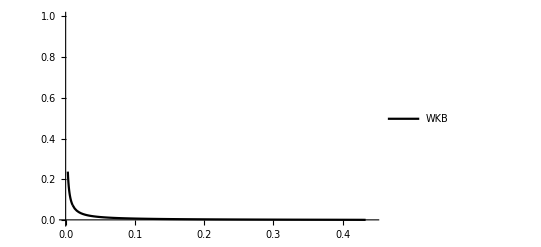

```mathematica
Clear[WKB1β]
WKB1β=ListPlot[{(*α11,*)α112a,α113},PlotRange->{{0,Mmax+0.01},{-0.01,1}},(*FrameLabel->{Style["M",15],Style["|Re(ω)|",15]},AxesOrigin->{0,0},Frame->True,Axes->False,*)PlotStyle->{Black},Joined->True,PlotLegends->Placed[{"WKB"},{Right,Top}]]
```

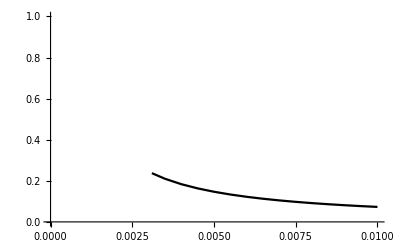

```mathematica
plotinWKBminβ=ListPlot[{(*α11,*)α112a},PlotRange->{{0,0.01},{0,1}},(*FrameLabel->{Style["M",15],Style["|Re(ω)|",15]},AxesOrigin->{0,0},Frame->True,Axes->False,*)PlotStyle->{Black},Joined->True(*PlotLegends->Placed[{"l=1","l=10","l=25","l=50","l=100"},{Right,Top}],*)]
```

```mathematica
plotindSβ=Plot[ImωdSoverκm[M,(*n*)0,(*l*)1,(*μ*)0.5,(*ξ*)0.5],{M,0,0.0031},PlotRange->{{0,0.01},{0,0.6}},Frame->True,PlotStyle->{Red},FrameTicks->{{{0,0.5,1},None},{{0,0.005,0.01},None}},GridLines->{{},{{0.5,{Red,Dashed,Thin}}}},ImageSize->110];
plotinminβ=Show[plotindSβ,plotinWKBminβ]
```

-Graphics-

```mathematica
plotinPTβ=Plot[M,{M,0.5,1},PlotRange->{{0.4,Mmax+0.001},{-0.00005,0.0004}},Frame->True,PlotStyle->{Blue},FrameTicks->{{{0,0.0002,0.0004},None},{{0.4,0.41,0.42,0.43},None}},Epilog->{PointSize[Medium],Point[{{0.43301,3.0958442721023882*^-6}},VertexColors->{Blue}]},(*GridLines->{{{0.0255,Dashed}},{{0.0796776,Dashed}}},*)ImageSize->110]
```

-Graphics-

```mathematica
plotinMaxβ=Show[plotinPTβ,plotinWKBMaxβ]
```

-Graphics-

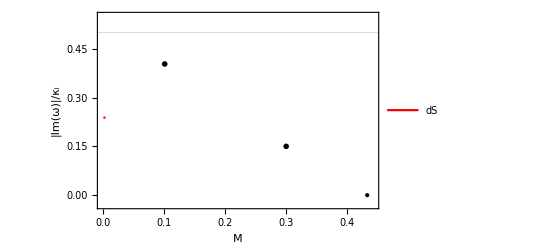

```mathematica
dSβ=Plot[ImωdSoverκm[M,(*n*)0,(*l*)1,(*μ*)0.5,(*ξ*)0.5],{M,0,0.0035},FrameLabel->{Style["M",12],Style["|Im(ω)|/κ_i",12]}(*,RotateLabel->False*),Frame->True,Axes->False,AxesOrigin->{0,0},PlotStyle->{Blue,Red},PlotRange->{{-0.001,Mmax+0.01},{-0.03,0.55}},GridLines->{{},{{0.5,{Red,Dashed,Thin}}}},Epilog->{(*Inset[Style["M_1",12],{0.12,-0.006}],*)Inset[plotinminβ,{0.1007,0.403}],Inset[plotinMaxβ,{0.3,0.15}],{PointSize[Medium],Point[{{0.43301,3.0958442721023882*^-6}},VertexColors->{Blue}]}},PlotLegends->Placed[{"dS"},{Right,Top}]]
```

```mathematica
PTβ=Plot[PT[M],{M,0.4,Mmax},PlotStyle->{Blue},PlotLegends->Placed[{"NE"},{Right,Top}]]
```

-Graphics-

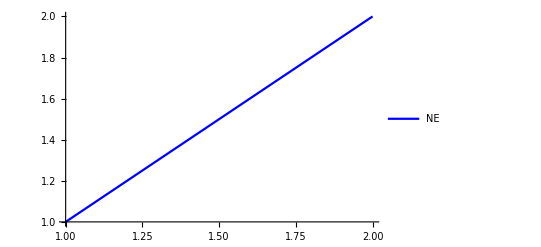

```mathematica
PTLegend=Plot[M,{M,1,2},PlotStyle->{Blue},PlotLegends->Placed[{"NE"},{Right,Top}]]
```

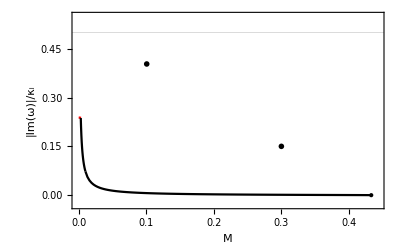

```mathematica
Show[dSβ,WKB1β,PTLegend(*,PTβ*)]
```